## Solution CP-11: Higher-dimensional systems

## Higher-dimensional systems

For an overview of the relevant Mathematica commands, refer to chapter 12 of the tutorial, and also to chapters 9 & 10, since many commands are very similar to those used in linear systems (e.g., how to plot time and phase diagrams).

```mathematica
Quit[]
```

### Exercise 11-1: Chaos in a Three-Species Food Chain (Hastings & Powell, Ecology 72:896-903, 1991)

A three-species food chain: ⅆx/ⅆt=x·(1-x)-f_1(x)·y, ⅆy/ⅆt=f_1(x)·y-f_2(y)·z-d_1 y, and ⅆz/ⅆt=f_2(y)·z-d_2 z; with f_1(x)=a_1 x/(1+b_1 x) and f_2(y)=a_2 y/(1+b_2 y), fixed parameters a_1=5.0, a_2=0.1, b_2=2.0, d_1=0.4, d_2=0.01, and variable parameter b_1=2.0  to  6.2.

```mathematica
f1[x_]:=a1*x/(1+b1*x)
f2[y_]:=a2*y/(1+b2*y)
param={a1->5.0, a2->0.1, b2->2.0, d1->0.4, d2->0.01};
eq1=D[x[t],t]==x[t]*(1-x[t])-f1[x[t]]*y[t]/.param
eq2=D[y[t],t]==f1[x[t]]*y[t]-f2[y[t]]*z[t]-d1*y[t]/.param
eq3=D[z[t],t]==f2[y[t]]*z[t]-d2*z[t]/.param
```

x'[t]==(1-x[t]) x[t]-(5. x[t] y[t])/(1+b1 x[t])

y'[t]==-0.4 y[t]+(5. x[t] y[t])/(1+b1 x[t])-(0.1 y[t] z[t])/(1+2. y[t])

z'[t]==-0.01 z[t]+(0.1 y[t] z[t])/(1+2. y[t])

(a/b) Reproduce Figure 2 with Mathematica: Construct time plots and a 3D phase plot of the system with b_1=3.0.

```mathematica
timePhasePlot[b1_, x0_, y0_, z0_, minT_, maxT_]:=Module[{a1=5.0, a2=0.1, b2=2.0, d1=0.4, d2=0.01, f1, f2, eq1, eq2, eq3, init, solX, solY, solZ, plotX, plotY, plotZ, phase},
f1[x_]:=a1*x/(1+b1*x);
f2[y_]:=a2*y/(1+b2*y);
eq1=D[x[t],t]==x[t]*(1-x[t])-f1[x[t]]*y[t];
eq2=D[y[t],t]==f1[x[t]]*y[t]-f2[y[t]]*z[t]-d1*y[t];
eq3=D[z[t],t]==f2[y[t]]*z[t]-d2*z[t];
init={x[0]==x0, y[0]==y0, z[0]==z0};
{solX, solY, solZ}=NDSolveValue[{eq1, eq2, eq3, init},{x[t],y[t],z[t]},{t, minT,maxT}];
plotX=Plot[solX, {t, minT, maxT}, AxesLabel->{"t", "X"}, PlotRange->Full];
plotY=Plot[solY, {t, minT, maxT}, AxesLabel->{"t", "Y"}, PlotRange->Full, PlotStyle->Orange];
plotZ=Plot[solZ, {t,  minT, maxT}, AxesLabel->{"t", "Z"}, PlotRange->Full, PlotStyle->Purple];
phase=ParametricPlot3D[{solX, solY, solZ}, {t,  minT, maxT}, BoxRatios->1, AxesLabel->{"X", "Y", "Z"}, PlotStyle->Gray];
GraphicsGrid[{{plotX,plotY},{plotZ,phase}}, ImageSize->Large]
]
```

```mathematica
timePhasePlot[3.0, 1.0,1.0,1.0,5000,6500]
```

-Graphics-

(c) Study what happens to your plots of (b) when you vary b1 in the same way as indicated in Table 1.

```mathematica
Manipulate[timePhasePlot[b1,x0,y0,z0,tmin,tmax],{{b1,3},2.0,6.2,0.1},{{x0,0.75},0,1},{{y0,0.175},0,.5},{{z0,7},5,10},{tmin,5000},{tmax,6500}]
```

Convergence to equilibrium at b1 < 2.2.
Limit cycle: 2-cycle oscillations at b1=2.2, 4-cycle oscillations at b1=2.3.  The higher b1, the more chaotic the system becomes.

(d) Reproduce Figure 3.

```mathematica
initSensitivityX[b1_, x0_, y0_, z0_, minT_, maxT_, ϵx_]:=Module[{a1=5.0, a2=0.1, b2=2.0, d1=0.4, d2=0.01, f1, f2, eq1, eq2, eq3, init1, init2, solX1, solX2, solY, solZ, plotX},
f1[x_]:=a1*x/(1+b1*x);
f2[y_]:=a2*y/(1+b2*y);
eq1=D[x[t],t]==x[t]*(1-x[t])-f1[x[t]]*y[t];
eq2=D[y[t],t]==f1[x[t]]*y[t]-f2[y[t]]*z[t]-d1*y[t];
eq3=D[z[t],t]==f2[y[t]]*z[t]-d2*z[t];
init1={x[0]==x0, y[0]==y0, z[0]==z0};
init2={x[0]==x0-ϵx, y[0]==y0, z[0]==z0};
{solX1, solY, solZ}=NDSolveValue[{eq1, eq2, eq3, init1},{x[t],y[t],z[t]},{t, minT,maxT}];
{solX2, solY, solZ}=NDSolveValue[{eq1, eq2, eq3, init2},{x[t],y[t],z[t]},{t, minT,maxT}];
plotX=Plot[{solX1, solX2}, {t, minT, maxT}, AxesLabel->{"t", "X"}, PlotRange->Full, PlotStyle->{Thick, Dashed}]
]
```

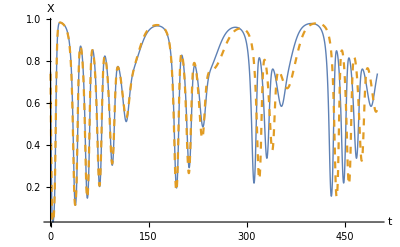

```mathematica
initSensitivityX[3.0, 0.75, 0.5, 8.0, 0, 500, 0.01]
```

(e) Try to reproduce Figure 4.

“Successive maxima” here may means successive peaks of the oscillations (in the time plot). Find these using sliding windows technique. For example, windows with 3 z-value points, length of 2*eps unit of time: {z[t-eps], z[t], z[t+eps]} A maximum or peak would correspond to a maximum middle point (2nd point of the triplet is the maximum of the triplet)

```mathematica
Quit[]
```

```mathematica
solveZ[b1_, x0_, y0_, z0_, minT_, maxT_]:=Module[{a1=5.0, a2=0.1, b2=2.0, d1=0.4, d2=0.01, f1, f2, eq1, eq2, eq3, init, solX, solY, solZ},f1[x_]:=a1*x/(1+b1*x);
f2[y_]:=a2*y/(1+b2*y);
eq1=D[x[t],t]==x[t]*(1-x[t])-f1[x[t]]*y[t];
eq2=D[y[t],t]==f1[x[t]]*y[t]-f2[y[t]]*z[t]-d1*y[t];
eq3=D[z[t],t]==f2[y[t]]*z[t]-d2*z[t];
init={x[0]==x0, y[0]==y0, z[0]==z0};
{solX, solY, solZ}=NDSolveValue[{eq1, eq2, eq3, init},{x[t],y[t],z[t]},{t, minT,maxT}];
solZ
]
successiveMaxZ[b1_, x0_, y0_, z0_, minT_, maxT_, timeStep_]:=Module[{solZ,tHead, window, maxZ},
solZ=solveZ[b1, x0, y0, z0, minT, maxT];
maxZ={};
tHead=minT;
While[tHead+2*timeStep<=maxT,
window={N[solZ/.t->tHead], N[solZ/.t->tHead+timeStep], N[solZ/.t->tHead+2*timeStep]};
If[window[[2]]==Max[window], maxZ=Append[maxZ,window[[2]]]];
tHead=tHead+timeStep;
];
maxZ=Union[maxZ];
Table[{b1, maxZ[[k]]},{k, 1, Length[maxZ]}]
]
```

```mathematica
epsZ = 0.05;
epsA=0.01;
ptsA=Flatten[ParallelTable[successiveMaxZ[b1,0.75,0.175,7,5000,6000 , epsZ],{b1,2.0, 3.2, epsA}],1];
```

```mathematica
epsB=0.01;
ptsB=Flatten[ParallelTable[successiveMaxZ[b1,0.75,0.175,7,15000,16000 , epsZ],{b1,3.2, 6.2, epsB}],1];
```

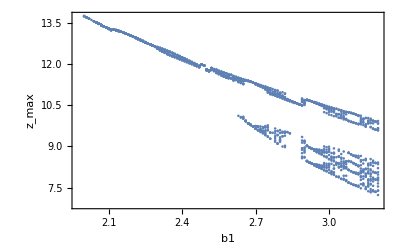

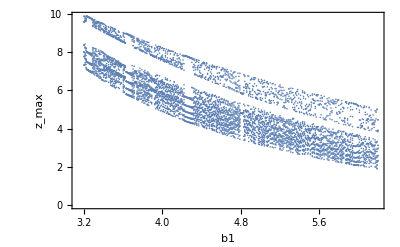

```mathematica
ListPlot[ptsA, Frame->True, FrameLabel->{"b1", "z_max"}]
ListPlot[ptsB, Frame->True, FrameLabel->{"b1", "z_max"}]
```

### Exercise 11-2: Omnivory Creates Chaos in Simple Food Web Models (Tanabe & Namba (Ecology 86:3411-3414, 2005)

```mathematica
Quit[]
```

A simple food web model: (ⅆ N_1)/ⅆt=N_1·(b_1-a_11 N_1-a_12 N_2-a_13 N_3), (ⅆ N_2)/ⅆt=N_2·(-b_2+a_21 N_1-a_23 N_3), and (ⅆ N_3)/ⅆt=N_3·(-b_3+a_31 N_1+a_32 N_2).

(e) Try to reproduce Figure 1 with parameters b_1=5, b_2=1, b_3=1.2, a_11=0.4, a_12=a_21=a_23=a_32=1.

```mathematica
param={b1->5 ,b2->1,b3->1.2,a11->0.4,a12->1,a21->1,a23->1,a32->1};
rhs1=n1*(b1-a11*n1-a12*n2-a13*n3)/.param;
rhs2=n2*(-b2+a21*n1-a23*n3)/.param;
rhs3=n3*(-b3+a31*n1+a32*n2)/.param;
```

```mathematica
eqVal=NSolveValues[rhs1==0&&rhs2==0&&rhs3==0,{n1,n2,n3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.,1.2,-1.},{(1. (3.8+1. a13))/(0.4+1. a13-1. a31),-(1. (-0.48-1.2 a13+5. a31+1. a13 a31))/(0.4+1. a13-1. a31),(1. (3.4+1. a31))/(0.4+1. a13-1. a31)},{1.2/a31,0.,(5. (-0.096+1. a31))/(a13 a31)},{12.5,0.,0.},{1.,4.6,0.},{0.,0.,0.}}

```mathematica
j=D[{rhs1,rhs2,rhs3},{{n1,n2,n3}}];
MatrixForm[j]
```

(5-0.8 n1-n2-a13 n3 | -n1 | -a13 n1
n2 | -1+n1-n3 | -n2
a31 n3 | n3 | -1.2+a31 n1+n2)

```mathematica
Re[Eigenvalues[j/.{n1->eqVal[[4,1]], n2->eqVal[[4,2]], n3->eqVal[[4,3]]}]] (*equilibrium {12.5, 0.,0.} is unstable*)
```

{11.5,-5.,-1.2+12.5 Re[a31]}

```mathematica
Re[Eigenvalues[j/.{n1->eqVal[[5,1]], n2->eqVal[[5,2]], n3->eqVal[[5,3]]}]](*equilibrium {1.,4.6,0.} is unstable since a31>0*)
```

{-0.2,-0.2,3.4+1. Re[a31]}

```mathematica
Re[Eigenvalues[j/.{n1->eqVal[[6,1]], n2->eqVal[[6,2]], n3->eqVal[[6,3]]}]](*equilibrium {0., 0.,0.} is unstable*)
```

{5.,-1.2,-1.}

```mathematica
Re[Eigenvalues[j2/.{a13->0.01, a31->0.01}]]
```

{-0.811013,-0.811013,-2.18797}

```mathematica
j2=j/.{n1->eqVal[[2,1]], n2->eqVal[[2,2]], n3->eqVal[[2,3]]};
stabCoexist={};
j3=j/.{n1->eqVal[[3,1]], n2->eqVal[[3,2]], n3->eqVal[[3,3]]};
preyEx={};
unstable={};
Do[
eq2=eqVal[[2]]/.{a13->x, a31->y};
realEig2=Re[Eigenvalues[j2/.{a13->x, a31->y}]];
If[eq2[[1]]>0&&eq2[[2]]>=0&&eq2[[3]]>0,If[realEig2[[1]]<0 && realEig2[[2]]<0 && realEig2[[3]]<0, If[eq2[[2]]!=0,AppendTo[stabCoexist,{x,y}],AppendTo[preyEx,{x,y}]], AppendTo[unstable, {x,y}]]];
eq3=eqVal[[3]]/.{a13->x, a31->y};
realEig3=Re[Eigenvalues[j3/.{a13->x, a31->y}]];
If[eq3[[1]]>0&&eq3[[3]]>0 &&realEig3[[1]]<0 && realEig3[[2]]<0 && realEig3[[3]]<0, AppendTo[preyEx,{x,y}]],
{x,0.11,10,0.1}, {y, 0.011, 1.0,0.01}
]
```

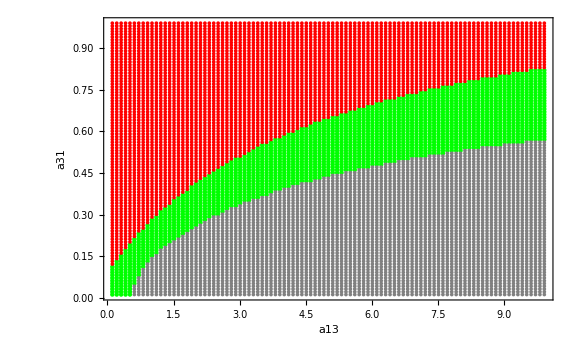

```mathematica
p1=ListPlot[stabCoexist, PlotStyle->Green];
p2=ListPlot[preyEx, PlotStyle->Red];
p3=ListPlot[unstable, PlotStyle->Gray];
Show[p1,p2,p3, PlotRange->All,Frame->True, FrameLabel->{Style["a13",FontSize->15],Style["a31",FontSize->15]}, ImageSize->Large]
```

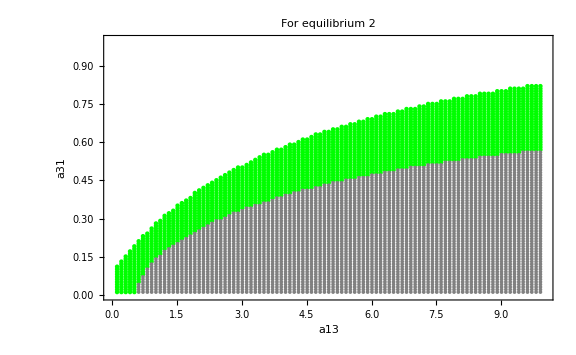

```mathematica
j2=j/.{n1->eqVal[[2,1]], n2->eqVal[[2,2]], n3->eqVal[[2,3]]};
stabCoexist={};
preyEx={};
unstable={};
Do[
eq2=eqVal[[2]]/.{a13->x, a31->y};
realEig2=Re[Eigenvalues[j2/.{a13->x, a31->y}]];
If[eq2[[1]]>0&&eq2[[2]]>=0&&eq2[[3]]>0,If[realEig2[[1]]<0 && realEig2[[2]]<0 && realEig2[[3]]<0, If[eq2[[2]]!=0,AppendTo[stabCoexist,{x,y}],AppendTo[preyEx,{x,y}]], AppendTo[unstable, {x,y}]]],
{x,0.11,10,0.1}, {y, 0.011, 1.0,0.01}
]
p1=ListPlot[stabCoexist, PlotStyle->Green];
p2=ListPlot[preyEx, PlotStyle->Red];
p3=ListPlot[unstable, PlotStyle->Gray];
Show[p1,p2,p3, PlotRange->{{0,10},{0,1.0}},PlotLabel->"For equilibrium 2",Frame->True, FrameLabel->{Style["a13",FontSize->15],Style["a31",FontSize->15]}, ImageSize->Large]
```

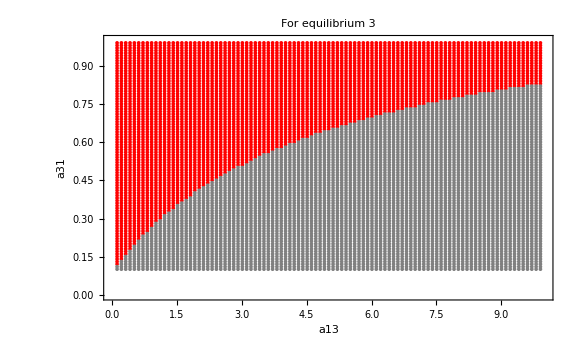

```mathematica
j3=j/.{n1->eqVal[[3,1]], n2->eqVal[[3,2]], n3->eqVal[[3,3]]};
stabCoexist={};
preyEx={};
unstable={};
Do[
eq3=eqVal[[3]]/.{a13->x, a31->y};
realEig3=Re[Eigenvalues[j3/.{a13->x, a31->y}]];
If[eq3[[1]]>0&&eq3[[3]]>0,If[realEig3[[1]]<0 && realEig3[[2]]<0 && realEig3[[3]]<0, AppendTo[preyEx,{x,y}], AppendTo[unstable, {x,y}]]],
{x,0.11,10,0.1}, {y, 0.011, 1.0,0.01}
]
p2=ListPlot[preyEx, PlotStyle->Red];
p3=ListPlot[unstable, PlotStyle->Gray];
Show[p2,p3, PlotRange->{{0,10},{0,1.0}},PlotLabel->"For equilibrium 3",Frame->True, FrameLabel->{Style["a13",FontSize->15],Style["a31",FontSize->15]}, ImageSize->Large]
```

(b) Reproduce their Fig. 2B (phase plot) and Fig. 2C (time plot) for a_13=10 and  a_31=0.1.  Vary the ‘bifurcation parameter’ a_13.

```mathematica
timePhasePlot[a13_,a31_,n10_,n20_,n30_,minT_,maxT_]:=Module[{b1=5 ,b2=1,b3=1.2,a11=0.4,a12=1,a21=1,a23=1,a32=1,
eq1, eq2, eq3, init,sol1,sol2,sol3,time,phase},
eq1=D[n1[t],t]==n1[t]*(b1-a11*n1[t]-a12*n2[t]-a13*n3[t]);
eq2=D[n2[t],t]==n2[t]*(-b2+a21*n1[t]-a23*n3[t]);
eq3=D[n3[t],t]==n3[t]*(-b3+a31*n1[t]+a32*n2[t]);
init={n1[0]==n10, n2[0]==n20, n3[0]==n30};
{sol1,sol2,sol3}=NDSolveValue[{eq1,eq2,eq3,init},{n1[t],n2[t],n3[t]},{t,minT,maxT}];
time=Plot[{sol1,sol2,sol3},{t,minT,maxT},PlotRange->{All, {-5,20}},Frame->True, FrameLabel->{Style["t", FontSize->12], Style["Population density", FontSize->12]}];
phase=ParametricPlot3D[{sol1, sol2,sol3},{t,minT,maxT},PlotRange->{{-5,20},{-5,20},{-5,20}},
BoxRatios->{1, 1, 1},AxesLabel->{"N1","N2","N3"}];
GraphicsRow[{time, phase}, ImageSize->Full]
]
```

NDSolveValue::ndsz: At t == 45.5647, step size is effectively zero; singularity or stiff system suspected.

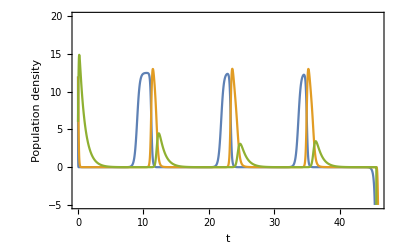

```mathematica
timePhasePlot[10,0.1,12,12,6,0,50]
```

```mathematica
Manipulate[timePhasePlot[a13, a31, n10,n20,n30,minT,maxT],{{a13,10},0.11,10,0.1},{{a31,0.1},0.011, 1.0,0.01}, {n10, 12.0}, {n20, 12.0}, {n30,6.0},{minT,0},{maxT,50}]
```